```mathematica
求阻尼摆的的运动——相图
```

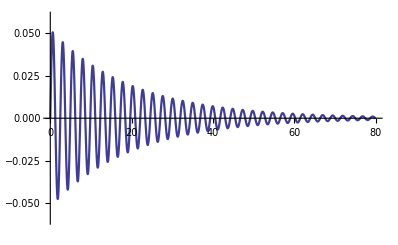

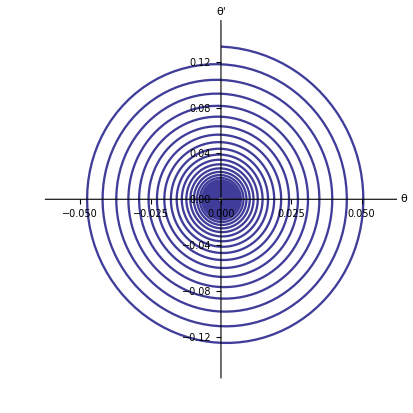

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v0=0.2;ω0=v0/L;η=0.1;tm=80;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]]-η*θ'[t],
θ[0]==0,θ'[0]==ω0},θ,{t,0,tm}];
θ=θ/.s[[1]];  
Plot[θ[t],{t,0,tm},PlotRange->{-0.06,0.06},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
ParametricPlot[{θ[t],θ'[t]},{t,0,tm},
PlotRange->{{-0.06,0.06},{-0.15,0.15}},
AxesLabel->{"θ","θ'"},AspectRatio->1,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,L,Ω,v0,ω0,η,tm,s,θ]
```

```mathematica
观察周期随时间的变化,指数拟合
```

2.45899 | 2.45892 | 2.45886 | 2.45881
2.45877 | 2.45875 | 2.45872 | 2.45871
2.45869 | 2.45868 | 2.45867 | 2.45867
2.45866 | 2.45866 | 2.45866 | 2.45865
2.45865 | 2.45865 | 2.45865 | 2.45865
2.45865 | 2.45865 | 2.45865 | 2.45865
2.45865 | 2.45865 | 2.45865 | 2.45865

{θ0→0.0521692,η0→0.0500021}

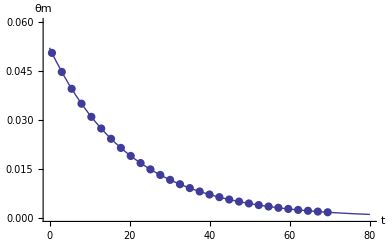

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v0=0.2;ω0=v0/L;η=0.1;tm=80;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]]-η*θ'[t],
θ[0]==0,θ'[0]==ω0},θ,{t,0,tm}];
θ=θ/.s[[1]];tc=2.48;peak={};
Do[
θm=FindMaximum[θ[t],{t,tc/4+(j-1) tc}];
AppendTo[peak,{t/.θm[[2]],θm[[1]]}],
{j,29}]
g1=ListPlot[peak,PlotRange->{0,0.06},
PlotStyle->PointSize[0.015]];
T=Table[peak[[j,1]]-peak[[j-1,1]],{j,2,29}];
Partition[T,4]//TableForm
peak=FindFit[peak,θ0 ⅇ^(-η0 t),{θ0,η0},t]
g2=Plot[θ0 ⅇ^(-η0 t)/.peak,{t,0,tm}];
Show[{g1,g2},AxesLabel->{"t","θm"}]
Clear[L,Ω,v0,ω0,η,tm,s,θ,tc,θm,peak]
```